# Sallen-Key Filter

```mathematica
Clear[ω,Q,α,τ,Α]
Q[α_] := 1/(3-α); (*Güte*)
τ:=1; (*R·C in s*)

A[ω_,α_] :=α/(1+ⅈ*ω*τ/Q[α]+(ⅈ*ω*τ)^2)  (*Übertragungsfunktion*)
Α = {1,1.268, 1.586, 2.234};(*Menge von α*)
pltLegends = Map["α = ",Α ]
```

{α = [1],α = [1.268],α = [1.586],α = [2.234]}

### Bode-Plot der Eingabe Daten

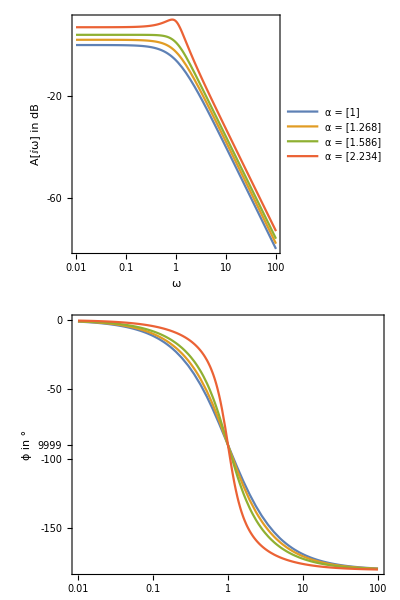

```mathematica
BodePlot[A[ω,Α], {ω,0.01,100},ImageSize->Medium, FrameLabel->{{"ω", "A[ⅈω] in dB"},{" ", "ϕ in °"}}, PlotLegends->pltLegends]
```

### Vergleich der Übertragungsfunktion bei ω=0 und ω=ω0

```mathematica
AbsA[ω_] = Abs[A[ω,Α]];
AbsAdB[ω_]:=N[20*Log[10,AbsA[ω]]];
```

```mathematica
Ares = AbsAdB[1/τ]
```

```mathematica
Azero = AbsAdB[0]
```

```mathematica
DeltaA = Ares-Azero
```

### Ortskurve

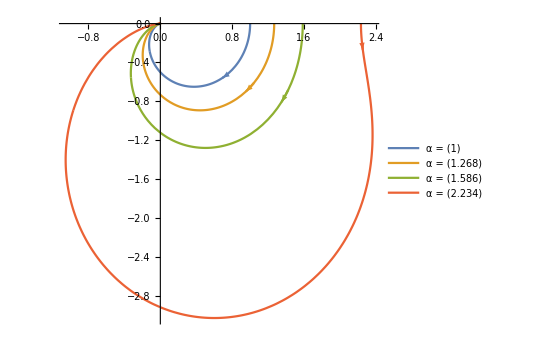

```mathematica
NyquistPlot[A[ω,Α], {ω,0.001,1000}, PlotLegends->pltLegends]
```